## Perturbation Theory:

If we introduce Interactions to the system i.e.

H =  -t ∑_(,,⟨ij⟩) a_i^†b_j + h.c. + ∑_ij V_ij n_i n_j

where n_i = c_i^†c_i for c = a/b. Using Wick’s theorem we can reduce the interaction term to terms which can be diagonalized easily. For that we need to calculate the Green function

G = (G_aa | G_ab
G_ba | G_bb) = (⟨a_i^†a_i⟩ | ⟨a_i^†b_i⟩
⟨b_i^†a_i⟩ | ⟨b_i^†b_i⟩)

We can calculate the expectations/contractions using Perturbation theory. It is easier to do the calculations in Momentum space.

H = H_0 + V
H_0 = ∑_k ϵ_k a_k^†a_k
V = ∑_(k_1,k_2,q) V(q)a_k_1^†b_k_2^†b_(k_2+q)b_(k_1-q)

where V(q) is the Fourier Transform of the potential

```mathematica
Assuming[q>0&&λ>0,Integrate[Integrate[Integrate[(e^2 ⅇ^(-I*q*rabs*Cos[θ]-λ*rabs))/rabs rabs^2 Sin[θ],{θ,0,π}],{rabs,0,Infinity}],{ϕ,0,2π}]];
Limit[%,λ->0];
Print["V(q) = " ,%]
```

V(q) = (4 e^2 π)/q^2

Lets define a function which will convert the function to polar co-ordinate and Integrate

```mathematica
Clear[Integrate3D];
Integrate3D[fun_,a_,Λ_]:=Integrate[Integrate[Integrate[(fun/.{Abs[a]:> a,a.b__:> a*b*Cos[θ]})*a^2 Sin[θ],{θ,0,π}],{a,0,Λ}],{ϕ,0,2π}]
```

```mathematica
Assuming[λ>0&&q∈Reals,Integrate3D[(e^2 Exp[I*a.q -λ*Abs[a]])/Abs[a],a,Infinity]];
Vq = Limit[%,λ->0]
```

(4 π e^2)/q^2

Green function for the free theory

G^0(k,iω_n) = (iω_n - σ.k)^-1

```mathematica
$LoadFeynArts = True;
<<FeynCalc`
$FAVerbose=0;
```

FeynCalc 9.2.0. For help, use the documentation center, check out the wiki or write to the mailing list.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207C, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

FeynArts 3.11 (2 Sep 2019) patched for use with FeynCalc, for documentation use the manual or visit www.feynarts.de.

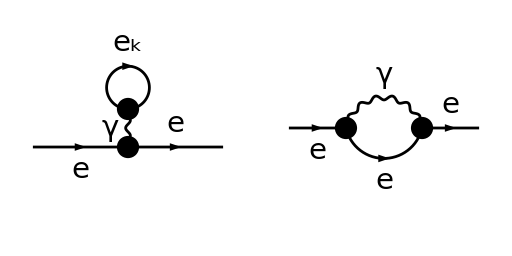

FeynArtsGraphics()(([] | []))

```mathematica
dia = CreateTopologies[1,1-> 1];
diagram = InsertFields[dia,{F[2,{1}]}->{F[2,{1}]},InsertionLevel -> {Classes}, GenericModel-> "Lorentz",Model -> "SM",ExcludeParticles->{S,V[2],V[3],F[1],F[3],F[4],U,T}];
Paint[diagram, ColumnsXRows -> {2, 1},Numbering -> None,SheetHeader->None,ImageSize->{512,256}]
```

G^(0)Σ^(1)G^(0)
Σ^(1) = Σ_1^(1) + Σ_2^(1) = V(q=0)G^(0)(k,ω) + V(q)G^(0)(k-q,ω)

#### Second Diagram

```mathematica
<<MatsubaraSum`
```

Notation::difform: The defined current default input format StandardForm differs from the current default output format TraditionalForm. The WorkingForm option will default to the current default output format, but the Notations, Symbolizations, and InfixNotations may behave differently than expected.

```mathematica
MatsubaraSum[1/(iω - Ek),iω∈Fermionic]
```

n_F[Ek]

After summing over the frequency we have

∑_k V(q=0)n_F(ϵ_k) + ∑_q V(q)n_F(ϵ_(k-q))

The first term is cancelled out by the uniform background positive charge density.

```mathematica
Assuming[k∈Reals,Integrate[Integrate[Integrate[(1/(q^2+k^2-2q.k)/.{Abs[q]:> r,q.b__:> r*b*Cos[θ]}),{ϕ,0,2π}],{θ,0,π}],r,PrincipalValue->True]]
```

$Aborted

```mathematica
1/(r^2+p^2-2a.p)/.{Abs[a]:> r,a.b__:> r*b*Cos[θ]}
```

```mathematica
Integrate[Normal[Series[1/(p^2-2 p r Cos[θ]+r^2),{p,0,2}]]Sin[θ],{θ,0,π}]
```

(2 (p^2+3 r^2))/(3 r^4)

```mathematica
Assuming[k∈Reals,Integrate[Integrate[(1/(q^2+k^2-2q.k)/.{Abs[q]:> r,q.b__:> r*b*Cos[θ]})r^2 Sin[θ],{ϕ,0,2π}],{θ,0,π}]]
```

$Aborted

```mathematica
Integrate[(1/(r^2+k^2-2q.k)/.{Abs[q]:> r,q.b__:> r*b*Cos[θ]})r^2 Sin[θ],{ϕ,0,2π}]
```

(2 π r^2 sin(θ))/(k^2-2 k r cos(θ)+r^2)

```mathematica
Integrate[%85,{θ,0,π}]
```

$Aborted

```mathematica
Assuming[r∈Reals&&k∈Reals&&{k^2+r^2+2k*r≠0,k^2-2k*r+r^2> 0},Integrate[%85,{θ,0,π}]]
```

ConditionalExpression[(π r log((k+r)^2/(k-r)^2))/k,k r (k+r)^2<0∨k r (k-r)^2>0]

```mathematica
Integrate[]
```